# How CD8 T cells in clusters kill the parasite (analysis of killing data from Cockburn et al. PNAS 2013) March 2018 - July 2018 - April 2021 - February 2022 - November 2022 - June 2023 - September 2023

```mathematica
(* These are additional in-house packages for plotting graphs and to do some data manipulations *)

Get["graphics-12-1.m"];
Get["tools-12.m"];
```

Fitting models to data

## Fitting simple models

### T cell dynamics: DDR model fitted to individual parasite data: main result

```mathematica
data=Import["Data_killing_23July2018-curated-final.csv","CSV"];
Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | Slice
2 | Parasite
3 | Background
4 | Tcells
5 | Exp [Py()]
6 | Parasite ID
7 | Original ID
8 | Time from Exp start (min)
9 | Time from T transfer (min)
10 | Original Parasite Intensity

```mathematica
parasiteID=Split[Drop[data[[All,6]],1]][[All,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
Clear[i]
threshold=Log10[1.25];

mousenumber=Table[
Cases[data,x_?(#[[6]]==parasiteID[[i]]&):>x[[5]]],{i,1,Length[parasiteID]}];

mousenumber=mousenumber[[All,1]];

parasiteIntensity=Table[
Cases[data,x_?(#[[6]]==parasiteID[[i]]&&#[[2]]≠"NA"&):>{x[[9]]/60,N[Log[10,x[[2]]/x[[3]]]]}],{i,1,Length[parasiteID]}];

TcellNumber=Table[Cases[data,x_?(#[[6]]==parasiteID[[i]]&):>{x[[9]]/60,x[[4]]}],{i,1,Length[parasiteID]}];

deathdata=Map[If[Length[Cases[#,x_?(#[[2]]<=threshold &)]]>0,1,0]&,parasiteIntensity]
tt=Map[Cases[#,x_?(#[[2]]<=threshold &)]&,parasiteIntensity];
deathtimedata=Table[If[deathdata[[i]]==1,Min[tt[[i]][[All,1]]],"NA"],{i,1,Length[deathdata]}];
```

{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0}

```mathematica
Cases[TcellNumber[[All,1]],x_?(#[[1]]≤4&)]
```

{{4,5},{4,0},{4,3},{4,5},{4,2},{4,0},{4,7},{4,8},{4,2}}

```mathematica
{
MyListPlot[parasiteIntensity,
PlotMarkers->None,
FrameLabel->{"hours since T cell transter","Log10 relative intensity"},
Epilog->{
mylegend2noS[{"n="<>ToString[Length[parasiteIntensity]]},{0,0.97}],
{dashings[[2]],Line[{{3,threshold},{13,threshold}}]}
},
PlotRange->{{3.8,14.1},{-0.05,1.41}},
Joined->True
],
Show[
MyListPlot[TcellNumber,
PlotMarkers->None,
FrameLabel->{"hours since T cell transter","T cell number/parasite"},
PlotRange->{{3.8,14.1},{-0.5,10}},
Joined->True
],
ListPlot[
Table[{If[deathdata[[i]]==1,{deathtimedata[[i]],TcellNumber[[i,1,2]]},{0,0}]},{i,1,Length[deathdata]}],
PlotMarkers->Map[If[#==1,{"†",Large},""]&,deathdata],
PlotStyle->Table[{{colors[[n]],dashings[[n]],Thickness[0.007]}},{n,1,32}],
Joined->False
]
]
}
MyGraphicsArray[%];
```

{-Graphics-,-Graphics-}

```mathematica
(* Fitting DDR model to all 32 parasites and T cells *)

T[t_,{lambda0_,lambda1_}]:=lambda0/lambda1*(1-Exp[-lambda1*t]);

ID=22;

datasetT=TcellNumber[[ID]];

fit=NonlinearModelFit[datasetT,T[t,{lambda0,lambda1}],{{lambda0,0.01},{lambda1,0.01}},t];
sol=fit["BestFitParameters"]
```

{lambda0→0.283545,lambda1→1.55938}

```mathematica
Show[
MyListPlot[{datasetT},
PlotRange->{{0,12},{-0.1,10.2}},
FrameLabel->{"time since T cell transfer, h","# of T cells/parasite"},
Epilog->{
mylegend2noS[{"ID="<>ToString[ID],"λ_0="<>ToString[MyRound[lambda0/.sol,2]]<>"/h","μ-λ_1="<>ToString[MyRound[lambda1/.sol,2]]<>"/h"},{0.0,0.97},FontColor->Table[Black,{3}]]
}
],
MyListPlot[{Table[{t,fit["BestFit"]},{t,0,12,0.05}]},
Joined->True,
PlotMarkers->None
]
]
```

-Graphics-

```mathematica
allfits=Map[NonlinearModelFit[#,T[t,{lambda0,lambda1}],{{lambda0,0.01},{lambda1,0.01}},t]&,TcellNumber];
allpars=Map[#["BestFitParameters"]&,allfits]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{lambda0→42.0974,lambda1→8.84655},{lambda0→1.73472×10^-18,lambda1→0.01},{lambda0→19.9084,lambda1→9.20071},{lambda0→93.9115,lambda1→19.4184},{lambda0→19.0335,lambda1→9.51673},{lambda0→5.20417×10^-18,lambda1→0.01},{lambda0→3.3598,lambda1→0.405077},{lambda0→2.70926,lambda1→0.185031},{lambda0→0.707981,lambda1→0.0825665},{lambda0→0.0512682,lambda1→2.4096},{lambda0→4.71166,lambda1→4.71166},{lambda0→0.872008,lambda1→0.258026},{lambda0→2.42159×10^-15,lambda1→-2.82892},{lambda0→2.54406×10^-14,lambda1→-2.73601},{lambda0→6.93889×10^-18,lambda1→0.01},{lambda0→6.93889×10^-18,lambda1→0.01},{lambda0→2.79035,lambda1→1.08381},{lambda0→0.174929,lambda1→-0.0978779},{lambda0→14.5859,lambda1→4.48065},{lambda0→0.0871637,lambda1→-0.197196},{lambda0→7.52242,lambda1→7.52242},{lambda0→0.283545,lambda1→1.55938},{lambda0→0.704125,lambda1→-0.00888728},{lambda0→0.524783,lambda1→0.46113},{lambda0→1.21431×10^-17,lambda1→0.01},{lambda0→5.85674,lambda1→5.85674},{lambda0→3.30637×10^-10,lambda1→-2.04168},{lambda0→0.0159567,lambda1→-0.289131},{lambda0→4.82118,lambda1→4.82118},{lambda0→1.56125×10^-17,lambda1→0.01},{lambda0→1.21431×10^-17,lambda1→0.01},{lambda0→1.21431×10^-17,lambda1→0.01}}

```mathematica
allpars0=Map[{lambda0,lambda1}/.#&,allpars];
tab=Prepend[Table[Join[{parasiteID[[i]],MyRound[Mean[TcellNumber[[i]][[All,2]]],1]},MyRound[allpars0[[i]],3]],{i,1,Length[parasiteID]}],{"ParasiteID","Mean T cell number","lambda0, 1/h","mu-lambda1,1/h"}];
%//TableForm
```

ParasiteID | Mean T cell number | lambda0, 1/h | mu-lambda1,1/h
1 | 4.8 | 42.097 | 8.847
2 | 0. | 0. | 0.01
3 | 2.2 | 19.908 | 9.201
4 | 4.8 | 93.912 | 19.418
5 | 2. | 19.033 | 9.517
6 | 0. | 0. | 0.01
7 | 7.2 | 3.36 | 0.405
8 | 8.9 | 2.709 | 0.185
9 | 2.9 | 0.708 | 0.083
10 | 0. | 0.051 | 2.41
11 | 1. | 4.712 | 4.712
12 | 3.1 | 0.872 | 0.258
13 | 0. | 0. | -2.829
14 | 0.1 | 0. | -2.736
15 | 0. | 0. | 0.01
16 | 0. | 0. | 0.01
17 | 2.6 | 2.79 | 1.084
18 | 3. | 0.175 | -0.098
19 | 3.3 | 14.586 | 4.481
20 | 1.4 | 0.087 | -0.197
21 | 1. | 7.522 | 7.522
22 | 0.2 | 0.284 | 1.559
23 | 5.5 | 0.704 | -0.009
24 | 1.1 | 0.525 | 0.461
25 | 0. | 0. | 0.01
26 | 1. | 5.857 | 5.857
27 | 0.2 | 0. | -2.042
28 | 0.7 | 0.016 | -0.289
29 | 1. | 4.821 | 4.821
30 | 0. | 0. | 0.01
31 | 0. | 0. | 0.01
32 | 0. | 0. | 0.01

```mathematica
Export["fit-DDRmodel-Tcellnumbers-32parasites.csv",tab,"CSV"];
```

```mathematica
Print["Median parameters = ",Median[allpars0]]
Print["Mean parameters = ",Mean[allpars0]]
```

Median parameters = {0.404164,0.133799}

Mean parameters = {7.02281,2.27187}

```mathematica
allfits={FittedModel[4.758620689655171 (1-ⅇ^(-8.84655240881126 t))],FittedModel[1.734723475976807*^-16 (1-ⅇ^(-0.01 t))],FittedModel[2.163793103448275 (1-ⅇ^(-9.200709716468566 t))],FittedModel[4.836206900345806 (1-ⅇ^(-19.418427393465976 t))],FittedModel[2. (1-ⅇ^(-9.516725801134486 t))],FittedModel[5.204170427930357*^-16 (1-ⅇ^(-0.010000000000000123 t))],FittedModel[8.29421921729476 (1-ⅇ^(-0.40507718671790116 t))],FittedModel[14.642149304574268 (1-ⅇ^(-0.18503144869013946 t))],FittedModel[8.574683376695113 (1-ⅇ^(-0.0825664879258128 t))],FittedModel[0.021276595755893336 (1-ⅇ^(-2.409604048581396 t))],FittedModel[1. (1-ⅇ^(-4.711660123425471 t))],FittedModel[3.379529513354816 (1-ⅇ^(-0.2580263433263454 t))],FittedModel[-8.560120631932642*^-16 (1-ⅇ^(2.8289223633456335 t))],FittedModel[-9.298440466268832*^-15 (1-ⅇ^(2.7360115024408453 t))],FittedModel[6.93889390390718*^-16 (1-ⅇ^(-0.01000000000000007 t))],FittedModel[6.93889390390718*^-16 (1-ⅇ^(-0.01000000000000007 t))],FittedModel[2.574575770151874 (1-ⅇ^(-1.08380795875684 t))],FittedModel[-1.7872134852822354 (1-ⅇ^(0.09787790398962258 t))],FittedModel[3.2553191489361675 (1-ⅇ^(-4.48064562374261 t))],FittedModel[-0.44201552189550963 (1-ⅇ^(0.19719602152920154 t))],FittedModel[1. (1-ⅇ^(-7.522423272669607 t))],FittedModel[0.18183173986849702 (1-ⅇ^(-1.5593826554166113 t))],FittedModel[-79.2284547025706 (1-ⅇ^(0.008887275507139768 t))],FittedModel[1.1380378824430355 (1-ⅇ^(-0.4611299536685901 t))],FittedModel[1.214306433183741*^-15 (1-ⅇ^(-0.010000000000000198 t))],FittedModel[1. (1-ⅇ^(-5.856743016395852 t))],FittedModel[-1.6194343158939783*^-10 (1-ⅇ^(2.041680947428564 t))],FittedModel[-0.05518829089084372 (1-ⅇ^(0.2891312846847088 t))],FittedModel[0.9999999999999999 (1-ⅇ^(-4.821182161526005 t))],FittedModel[1.5612511283790759*^-15 (1-ⅇ^(-0.010000000000000325 t))],FittedModel[1.214306433183741*^-15 (1-ⅇ^(-0.010000000000000198 t))],FittedModel[1.214306433183741*^-15 (1-ⅇ^(-0.010000000000000198 t))]};

allpars={{lambda0->42.09738732468805,lambda1->8.84655240881126},{lambda0->1.734723475976807*^-18,lambda1->0.01},{lambda0->19.908432231324216,lambda1->9.200709716468566},{lambda0->93.91153255414417,lambda1->19.418427393465976},{lambda0->19.033451602268972,lambda1->9.516725801134486},{lambda0->5.204170427930421*^-18,lambda1->0.010000000000000123},{lambda0->3.3597989865633138,lambda1->0.40507718671790116},{lambda0->2.709258097762695,lambda1->0.18503144869013946},{lambda0->0.7079814914895647,lambda1->0.0825664879258128},{lambda0->0.05126817127343033,lambda1->2.409604048581396},{lambda0->4.711660123425471,lambda1->4.711660123425471},{lambda0->0.8720076424944068,lambda1->0.2580263433263454},{lambda0->2.421591668861061*^-15,lambda1->-2.8289223633456335},{lambda0->2.5440640070472938*^-14,lambda1->-2.7360115024408453},{lambda0->6.938893903907228*^-18,lambda1->0.01000000000000007},{lambda0->6.938893903907228*^-18,lambda1->0.01000000000000007},{lambda0->2.7903457101131224,lambda1->1.08380795875684},{lambda0->0.17492870992141338,lambda1->-0.09787790398962258},{lambda0->14.585931498566358,lambda1->4.48064562374261},{lambda0->0.08716370237194818,lambda1->-0.19719602152920154},{lambda0->7.522423272669607,lambda1->7.522423272669607},{lambda0->0.2835452613551594,lambda1->1.5593826554166113},{lambda0->0.7041251049466882,lambda1->-0.008887275507139768},{lambda0->0.5247833560040573,lambda1->0.4611299536685901},{lambda0->1.214306433183765*^-17,lambda1->0.010000000000000198},{lambda0->5.856743016395852,lambda1->5.856743016395852},{lambda0->3.306368188372746*^-10,lambda1->-2.041680947428564},{lambda0->0.015956661444823057,lambda1->-0.2891312846847088},{lambda0->4.821182161526005,lambda1->4.821182161526005},{lambda0->1.5612511283791264*^-17,lambda1->0.010000000000000325},{lambda0->1.214306433183765*^-17,lambda1->0.010000000000000198},{lambda0->1.214306433183765*^-17,lambda1->0.010000000000000198}};

Table[
sol=allpars[[ID]];
Show[
MyListPlot[{TcellNumber[[ID]]},
PlotRange->{{0,12},{-0.2,10.2}},
FrameLabel->{"time since T cell transfer, h","# of T cells/parasite"},
BaseStyle->{FontSize->22},
Epilog->{
mylegend2[{"ID="<>ToString[ID]<> " (mouse "<>ToString[mousenumber[[ID]]]<>")"},{If[ID==8,0.35,0.08],If[ID==8,0.25,0.97],0.1,0.08},FontColor->Table[Black,{3}],FontSize->Table[16,{4}]],
mylegend[{"λ_0="<>ToString[MyRound[lambda0/.sol,2]]<>"/h, μ-λ_1="<>ToString[MyRound[lambda1/.sol,2]]<>"/h"},{If[ID==8,0.30,0.03],If[ID==8,0.17,0.88],0.1,0.06},FontColor->Table[Black,{3}],FontSize->Table[16,{4}]]
}
],
MyListPlot[{Table[{t,allfits[[ID]]["BestFit"]},{t,0,Max[TcellNumber[[ID]][[All,1]]],0.05}]},
Joined->True,
PlotMarkers->None
]
],{ID,1,Length[TcellNumber]}];

MyGraphicsArray[Partition[%,4]]
```

-Graphics-A | -Graphics-B | -Graphics-C | -Graphics-D
-Graphics-E | -Graphics-F | -Graphics-G | -Graphics-H
-Graphics-I | -Graphics-J | -Graphics-K | -Graphics-L
-Graphics-M | -Graphics-N | -Graphics-O | -Graphics-P
-Graphics-Q | -Graphics-R | -Graphics-S | -Graphics-T
-Graphics-U | -Graphics-V | -Graphics-W | -Graphics-X
-Graphics-Y | -Graphics-AA | -Graphics-AB | -Graphics-AC
-Graphics-AD | -Graphics-AE | -Graphics-AF | -Graphics-AG

```mathematica
Export["fit-DDRmodel-Tcellnumbers-32parasites.pdf",%,"PDF"];
```

### VI dynamics: ODE models + T cell dynamics from the DDR model: main result

```mathematica
data=Import["Data_killing_23July2018-curated-final.csv","CSV"];
Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | Slice
2 | Parasite
3 | Background
4 | Tcells
5 | Exp [Py()]
6 | Parasite ID
7 | Original ID
8 | Time from Exp start (min)
9 | Time from T transfer (min)
10 | Original Parasite Intensity

```mathematica
parasiteID=Split[Drop[data[[All,6]],1]][[All,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
Clear[i]
threshold=Log10[1.25];

mousenumber=Table[
Cases[data,x_?(#[[6]]==parasiteID[[i]]&):>x[[5]]],{i,1,Length[parasiteID]}];

mousenumber=mousenumber[[All,1]];

parasiteIntensity=Table[
Cases[data,x_?(#[[6]]==parasiteID[[i]]&&#[[2]]≠"NA"&):>{x[[9]]/60,N[Log[10,x[[2]]/x[[3]]]]}],{i,1,Length[parasiteID]}];

TcellNumber=Table[Cases[data,x_?(#[[6]]==parasiteID[[i]]&):>{x[[9]]/60,x[[4]]}],{i,1,Length[parasiteID]}];

deathdata=Map[If[Length[Cases[#,x_?(#[[2]]<=threshold &)]]>0,1,0]&,parasiteIntensity]
tt=Map[Cases[#,x_?(#[[2]]<=threshold &)]&,parasiteIntensity];
deathtimedata=Table[If[deathdata[[i]]==1,Min[tt[[i]][[All,1]]],"NA"],{i,1,Length[deathdata]}];
```

{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0}

```mathematica
Clear[ssrV2,parV,array,TT,tmin,tmax,n];

ssrV2[array_,parV_/;VectorQ[parV,NumericQ],type___]:=Module[{x0,r,k,n,h,ff0,result,x,xx,sol,tmax},
{x0,r,k,n}=parV;
tmax=N[Max[datasetT[[All,1]]]];
sol=NDSolve[
{x'[t]==r*x[t]-k*TT[t]^n*x[t],x[0]==x0},
{x[t]},
{t,0,tmax},
Method->Automatic
];

xx[t1_]:=First[x[t]/.sol]/.t->t1;

result=
Which[
type==1,Map[(Log[10,xx[#[[1]]]]-#[[2]])&,array],
type==2,Total[Map[(Log[10,xx[#[[1]]]]-#[[2]])^2&,array]],
type==3,Log10[xx[t]],
type==4,Table[{t,Log10[xx[t]]},{t,0,tmax,(tmax)/300}]
];
Clear[xx,sol];
result
];
```

```mathematica
T[t_,{lambda0_,lambda1_}]:=lambda0/lambda1*(1-Exp[-lambda1*t]);

allpars={{lambda0->42.09738732468805,lambda1->8.84655240881126},{lambda0->1.734723475976807*^-18,lambda1->0.01},{lambda0->19.908432231324216,lambda1->9.200709716468566},{lambda0->93.91153255414417,lambda1->19.418427393465976},{lambda0->19.033451602268972,lambda1->9.516725801134486},{lambda0->5.204170427930421*^-18,lambda1->0.010000000000000123},{lambda0->3.3597989865633138,lambda1->0.40507718671790116},{lambda0->2.709258097762695,lambda1->0.18503144869013946},{lambda0->0.7079814914895647,lambda1->0.0825664879258128},{lambda0->0.05126817127343033,lambda1->2.409604048581396},{lambda0->4.711660123425471,lambda1->4.711660123425471},{lambda0->0.8720076424944068,lambda1->0.2580263433263454},{lambda0->2.421591668861061*^-15,lambda1->-2.8289223633456335},{lambda0->2.5440640070472938*^-14,lambda1->-2.7360115024408453},{lambda0->6.938893903907228*^-18,lambda1->0.01000000000000007},{lambda0->6.938893903907228*^-18,lambda1->0.01000000000000007},{lambda0->2.7903457101131224,lambda1->1.08380795875684},{lambda0->0.17492870992141338,lambda1->-0.09787790398962258},{lambda0->14.585931498566358,lambda1->4.48064562374261},{lambda0->0.08716370237194818,lambda1->-0.19719602152920154},{lambda0->7.522423272669607,lambda1->7.522423272669607},{lambda0->0.2835452613551594,lambda1->1.5593826554166113},{lambda0->0.7041251049466882,lambda1->-0.008887275507139768},{lambda0->0.5247833560040573,lambda1->0.4611299536685901},{lambda0->1.214306433183765*^-17,lambda1->0.010000000000000198},{lambda0->5.856743016395852,lambda1->5.856743016395852},{lambda0->3.306368188372746*^-10,lambda1->-2.041680947428564},{lambda0->0.015956661444823057,lambda1->-0.2891312846847088},{lambda0->4.821182161526005,lambda1->4.821182161526005},{lambda0->1.5612511283791264*^-17,lambda1->0.010000000000000325},{lambda0->1.214306433183765*^-17,lambda1->0.010000000000000198},{lambda0->1.214306433183765*^-17,lambda1->0.010000000000000198}};
```

```mathematica
(* Fitting the data for 1 parasite at a time *)

ID=18;


datasetT=Cases[parasiteIntensity[[ID]],x_?(#[[2]]≥VImin&)];

TT[t_]=T[t,{lambda0,lambda1}/.allpars[[ID]]];
eps=10;
pow=2;
VImin=0.1;


MyListPlot[{TcellNumber[[ID]]},
PlotMarkers->None,
Epilog->mylegend2noS[{"ID="<>ToString[ID]},{0.7,0.95}],
FrameLabel->{"hours since T cell transter","T cell numbers"},
PlotStyle->{{colors[[ID]],dashings[[ID]],Thickness[0.007]}},
PlotRange->{{0,13},{-0.1,10}},
Joined->True
]
```

-Graphics-

```mathematica
(* mass-action killing *)

Clear[x0,r,k,n];


AllParsAll={
{{x0,99.08514045602925,1},{r,0,1},{k,0.17439608242650215,0},{n,1,1}},
{{x0,5.332097809266228,0},{r,0,1},{k,0.,1},{n,1,1}},
{{x0,2.0901409309761183,0},{r,0,1},{k,0.011407657815126707,0},{n,1,1}},
{{x0,3.012516181010691,0},{r,0,1},{k,0.0064051671035984655,0},{n,1,1}},
{{x0,1.9949560616910083,0},{r,0,1},{k,0.002252776929836142,0},{n,1,1}}, (* ID=5 *)
{{x0,5.830956037143223,0},{r,0,1},{k,0.,1},{n,1,1}},
{{x0,2.8901490268495897,0},{r,0,1},{k,0.022891713273055215,0},{n,1,1}},
{{x0,4.924111292903079,0},{r,0,1},{k,0.06926917369310584,0},{n,1,1}},
{{x0,1.6614542360149913,0},{r,0,1},{k,0.014071910911853114,0},{n,1,1}},
{{x0,3.4974227821572317,0},{r,0,1},{k,6.659895997795028*^-15,0},{n,1,1}},  (* ID=10 *)
{{x0,4.710684685213522,0},{r,0,1},{k,0.00444147406446986,0},{n,1,1}},
{{x0,6.120420949749093,0},{r,0,1},{k,1.5037241797296461*^-18,0},{n,1,1}},
{{x0,2.4702942312892575,0},{r,0,1},{k,1.7471617688207244*^-23,0},{n,1,1}},
{{x0,5.303373233958356,0},{r,0,1},{k,0.2913097713565586,0},{n,1,1}},
{{x0,4.370999570654583,0},{r,0,1},{k,0.,1},{n,1,1}},                                  (* ID=15 *)
{{x0,7.047231732274569,0},{r,0,1},{k,0,1},{n,1,1}},
{{x0,13.413436722366031,0},{r,0,1},{k,0.036738351753008526,0},{n,1,1}},
{{x0,7.635291319728003,0},{r,0,1},{k,0.09517984176204938,0},{n,1,1}},
{{x0,40.511798191563564,0},{r,0,1},{k,0.09721469262832302,0},{n,1,1}},
{{x0,2.7222940678106284,0},{r,0,1},{k,0.03699348416242348,0},{n,1,1}}, (* ID=20 *)
{{x0,20.81927710843374,0},{r,0,1},{k,0.1764799862314121,0},{n,1,1}},
{{x0,78.89057785893269,0},{r,0,1},{k,1.9472684514662615,0},{n,1,1}},
{{x0,3.132706567781419,0},{r,0,1},{k,0.02539275975614883,0},{n,1,1}},
{{x0,5.595566568850018,0},{r,0,1},{k,0.10893843194017475,0},{n,1,1}},
{{x0,2.65658144097139,0},{r,0,1},{k,0,1},{n,1,1}},                                             (* ID=25 *)
{{x0,99,1},{r,0,1},{k,0.5335692110440381,0},{n,1,1}},
{{x0,3.0787023783529954,0},{r,0,1},{k,1.9579393129885644*^-7,0},{n,1,1}},
{{x0,5.482714181233141,0},{r,0,1},{k,0.30473239866662377,0},{n,1,1}},
{{x0,5.646715797933296,0},{r,0,1},{k,0,1},{n,1,1}},
{{x0,3.185993228651323,0},{r,0,1},{k,0.,1},{n,1,1}},                                                    (* ID=30 *)
{{x0,6.072966630544719,0},{r,0,1},{k,0.,1},{n,1,1}},
{{x0,2.235245540000953,0},{r,0,1},{k,0.,1},{n,1,1}}
};

AllPars=AllParsAll[[ID]];

{ParF,Par0,FixedPars}=Transpose[AllPars];

pars=Table[If[FixedPars[[i]]==0,ParF[[i]]^pow,Par0[[i]]],{i,1,Length[ParF]}];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
ParD=(ParF*(1-FixedPars)+Par0*FixedPars);
Print["Parameters to be fitted ",pars0[[All,1]]];
eps=8;

tStart=SessionTime[];
ssrV2[datasetT,Par0,2]
tEnd=SessionTime[];
Print["Calculated in ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];
```

Parameters to be fitted {k,x0}

0.360644

Calculated in 0.00175 sec or 0.0000292 min

```mathematica
Show[
MyListPlot[{parasiteIntensity[[ID]]},
PlotMarkers->None,
Epilog->{
mylegend2noS[{"ID="<>ToString[ID]},{0.01,0.95}],
{dashings[[2]],Line[{{0,Log10[1.25]},{13,Log10[1.25]}}]}
},
FrameLabel->{"hours since T cell transter","Log10 relative intensity"},
PlotStyle->{{Gray,dashings[[ID]],Thickness[0.007]}},
PlotRange->{{0,13},{0,2}},
Joined->True
],
MyListPlot[{ssrV2[datasetT,Par0,4]},Joined->True,PlotMarkers->None]
]
```

-Graphics-

```mathematica
tStart=SessionTime[];

sol=FindMinimum[
ssrV2[datasetT,pars,2]+0*10^(5*(x0-256)),
pars0,
MaxIterations->10^4,
AccuracyGoal->eps,
PrecisionGoal->eps,
Method->Automatic 
];

sol[[2]]=Map[ReplacePart[#,#[[2]]^pow,2]&,sol[[2]]];

Print[sol];

tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];

If[NumericQ[sol[[1]]],Par0=ParD/.sol[[2]]];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
Transpose[{ParF,Par0,FixedPars}]
```

{0.360644,{k→0.0951798,x0→7.63529}}

Simulations ran for 0.31908 sec or 0.005318 min

{{x0,7.63529,0},{r,0,1},{k,0.0951798,0},{n,1,1}}

```mathematica
Tmean=Mean[TcellNumber[[ID]][[All,2]]];
Show[
MyListPlot[{parasiteIntensity[[ID]],datasetT},
PlotMarkers->None,
Epilog->{
mylegend2noS[{"ID="<>ToString[ID]<>" (T̄="<>ToString[MyRound[Tmean,2]]<>")","VI_0="<>ToString[MyRound[x0/.sol[[2]],2]]<>", r=0, k="<>If[NumericQ[k/.sol[[2]]],ToString[MyRound[k/.sol[[2]],3]]<>"/h","NA"]},{0.0,0.97},
FontColor->{Black,Black,Black}],
{dashings[[2]],Line[{{0,Log10[1.25]},{13,Log10[1.25]}}]}
},
FrameLabel->{"hours since T cell transter","Vitality index (VI)"},
PlotStyle->{{GrayLevel[0.8],dashings[[ID]],Thickness[0.007]},{Red}},
PlotRange->{{0,12},{0,2}},
Joined->True
],
MyListPlot[{ssrV2[datasetT,Par0,4]},Joined->True,PlotMarkers->None]
]
```

-Graphics-

```mathematica
(* making plots *)

AllParsAll={
{{x0,99.08514045602925,1},{r,0,1},{k,0.17439608242650215,0},{n,1,1}},
{{x0,5.332097809266228,0},{r,0,1},{k,0.,1},{n,1,1}},
{{x0,2.0901409309761183,0},{r,0,1},{k,0.011407657815126707,0},{n,1,1}},
{{x0,3.012516181010691,0},{r,0,1},{k,0.0064051671035984655,0},{n,1,1}},
{{x0,1.9949560616910083,0},{r,0,1},{k,0.002252776929836142,0},{n,1,1}}, (* ID=5 *)
{{x0,5.830956037143223,0},{r,0,1},{k,0.,1},{n,1,1}},
{{x0,2.8901490268495897,0},{r,0,1},{k,0.022891713273055215,0},{n,1,1}},
{{x0,4.924111292903079,0},{r,0,1},{k,0.06926917369310584,0},{n,1,1}},
{{x0,1.6614542360149913,0},{r,0,1},{k,0.014071910911853114,0},{n,1,1}},
{{x0,3.4974227821572317,0},{r,0,1},{k,6.659895997795028*^-15,0},{n,1,1}},  (* ID=10 *)
{{x0,4.710684685213522,0},{r,0,1},{k,0.00444147406446986,0},{n,1,1}},
{{x0,6.120420949749093,0},{r,0,1},{k,1.5037241797296461*^-18,0},{n,1,1}},
{{x0,2.4702942312892575,0},{r,0,1},{k,1.7471617688207244*^-23,0},{n,1,1}},
{{x0,5.303373233958356,0},{r,0,1},{k,0.2913097729551747,0},{n,1,1}},
{{x0,4.370999570654583,0},{r,0,1},{k,0.,1},{n,1,1}},                                  (* ID=15 *)
{{x0,7.047231732274569,0},{r,0,1},{k,0,1},{n,1,1}},
{{x0,13.413436722366031,0},{r,0,1},{k,0.036738351753008526,0},{n,1,1}},
{{x0,7.635314478569408,0},{r,0,1},{k,0.09518009890569201,0},{n,1,1}},
{{x0,40.511798191563564,0},{r,0,1},{k,0.09721469262832302,0},{n,1,1}},
{{x0,2.7222940678106284,0},{r,0,1},{k,0.03699348416242348,0},{n,1,1}}, (* ID=20 *)
{{x0,20.81927710843374,0},{r,0,1},{k,0.1764799862314121,0},{n,1,1}},
{{x0,78.89057785893269,0},{r,0,1},{k,1.9472684514662615,0},{n,1,1}},
{{x0,3.132706567781419,0},{r,0,1},{k,0.02539275975614883,0},{n,1,1}},
{{x0,5.595566568850018,0},{r,0,1},{k,0.10893843194017475,0},{n,1,1}},
{{x0,2.65658144097139,0},{r,0,1},{k,0,1},{n,1,1}},                                             (* ID=25 *)
{{x0,99,1},{r,0,1},{k,0.5335692110440381,0},{n,1,1}},
{{x0,3.0787023783529954,0},{r,0,1},{k,1.9579393129885644*^-7,0},{n,1,1}},
{{x0,5.482714181233141,0},{r,0,1},{k,0.30473239866662377,0},{n,1,1}},
{{x0,5.646715797933296,0},{r,0,1},{k,0,1},{n,1,1}},
{{x0,3.185993228651323,0},{r,0,1},{k,0.,1},{n,1,1}},                                                    (* ID=30 *)
{{x0,6.072966630544719,0},{r,0,1},{k,0.,1},{n,1,1}},
{{x0,2.235245540000953,0},{r,0,1},{k,0.,1},{n,1,1}}
};
```

```mathematica
(* Exporting fits *)

AllParsAll0=Map[#[[All,2]][[{1,3}]]&,AllParsAll];
tab=Prepend[Table[Join[{parasiteID[[i]],MyRound[Mean[TcellNumber[[i]][[All,2]]],1]},MyRound[AllParsAll0[[i]],3]],{i,1,Length[parasiteID]}],{"ParasiteID","Mean T cell number","VI(0)","k,1/h"}];
%//TableForm
```

ParasiteID | Mean T cell number | VI(0) | k,1/h
1 | 4.8 | 99.085 | 0.174
2 | 0. | 5.332 | 0.
3 | 2.2 | 2.09 | 0.011
4 | 4.8 | 3.013 | 0.006
5 | 2. | 1.995 | 0.002
6 | 0. | 5.831 | 0.
7 | 7.2 | 2.89 | 0.023
8 | 8.9 | 4.924 | 0.069
9 | 2.9 | 1.661 | 0.014
10 | 0. | 3.497 | 0.
11 | 1. | 4.711 | 0.004
12 | 3.1 | 6.12 | 0.
13 | 0. | 2.47 | 0.
14 | 0.1 | 5.303 | 0.291
15 | 0. | 4.371 | 0.
16 | 0. | 7.047 | 0.
17 | 2.6 | 13.413 | 0.037
18 | 3. | 7.635 | 0.095
19 | 3.3 | 40.512 | 0.097
20 | 1.4 | 2.722 | 0.037
21 | 1. | 20.819 | 0.176
22 | 0.2 | 78.891 | 1.947
23 | 5.5 | 3.133 | 0.025
24 | 1.1 | 5.596 | 0.109
25 | 0. | 2.657 | 0.
26 | 1. | 99. | 0.534
27 | 0.2 | 3.079 | 0.
28 | 0.7 | 5.483 | 0.305
29 | 1. | 5.647 | 0.
30 | 0. | 3.186 | 0.
31 | 0. | 6.073 | 0.
32 | 0. | 2.235 | 0.

```mathematica
Export["fit-VIdynamics-mass-action-DDRmodel-Tcellnumbers-32parasites.csv",tab,"CSV"];
```

```mathematica
(* Plotting all fits *)

allfigsVI=Table[
Par0=AllParsAll[[ID]][[All,2]];
datasetT=Cases[parasiteIntensity[[ID]],x_?(#[[2]]≥VImin&)];
TT[t_]=T[t,{lambda0,lambda1}/.allpars[[ID]]];
tmax=N[Max[datasetT[[All,1]]]];
Tmean=Mean[TcellNumber[[ID]][[All,2]]];
Show[
MyListPlot[{parasiteIntensity[[ID]],datasetT},
PlotMarkers->None,
Epilog->{
mylegend[{"ID="<>ToString[ID]<>" (T̄="<>ToString[MyRound[Tmean,2]]<>")","VI_0="<>ToString[MyRound[Par0[[1]],2]]<>", r=0, k="<>ToString[MyRound[Par0[[3]],3]]<>"/h"},{0.05,0.97,0.09,0.05},
FontColor->{Black,Red,Black},DashingStyle->{dashings[[1]],dashings[[1]],dashings[[1]]},FontSize->Table[16,{4}]],
{dashings[[2]],Line[{{0,Log10[1.25]},{13,Log10[1.25]}}]}
},
BaseStyle->{FontSize->20},
FrameLabel->{"hours since T cell transter","Vitality index (VI)"},
PlotStyle->{{GrayLevel[0.8],dashings[[ID]],Thickness[0.007]},{Black}},
PlotRange->{{0,12},{0,2}},
Joined->True
],
MyListPlot[{ssrV2[datasetT,Par0,4]},Joined->True,PlotMarkers->None,PlotStyle->{{Red,Thickness[0.007]}}]
],{ID,1,Length[AllParsAll]}]

MyGraphicsArray[Partition[allfigsVI,UpTo[4]]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["fit-VIdynamics-DDRmodel-32parasites.pdf",%,"PDF"]
```

/Users/vitaly/research/immunology/malaria/killing-in-clusters/figs/fit-VIdynamics-DDRmodel-32parasites.pdf

```mathematica
(* Parasite ID with no killing/low kill rate k *)

tempdata0=Transpose[{parasiteID,mousenumber,Map[N[Mean[#[[All,2]]]]&,TcellNumber],Map[#[[3,2]]&,AllParsAll]}];
Cases[tempdata0,x_?(#[[4]]<10^-3&)]//TableForm
```

2 | 1 | 0. | 0.
6 | 1 | 0. | 0.
10 | 2 | 0.0212766 | 6.6599×10^-15
12 | 2 | 3.10638 | 1.50372×10^-18
13 | 2 | 0.0212766 | 1.74716×10^-23
15 | 2 | 0. | 0.
16 | 2 | 0. | 0
25 | 3 | 0. | 0
27 | 3 | 0.153846 | 1.95794×10^-7
29 | 3 | 1. | 0
30 | 3 | 0. | 0.
31 | 3 | 0. | 0.
32 | 3 | 0. | 0.

```mathematica
(* Killing rate vs. T cell number *)

tempdata1=Transpose[{Map[N[Mean[#[[All,2]]]]&,TcellNumber],Map[#[[3,2]]&,AllParsAll],mousenumber}]
```

{{4.75862,0.174396,1},{0.,0.,1},{2.16379,0.0114077,1},{4.83621,0.00640517,1},{2.,0.00225278,1},{0.,0.,1},{7.2087,0.0228917,1},{8.90435,0.0692692,1},{2.93913,0.0140719,1},{0.0212766,6.6599×10^-15,2},{1.,0.00444147,2},{3.10638,1.50372×10^-18,2},{0.0212766,1.74716×10^-23,2},{0.0851064,0.29131,2},{0.,0.,2},{0.,0,2},{2.57447,0.0367384,2},{2.95745,0.0951801,2},{3.25532,0.0972147,2},{1.3913,0.0369935,4},{1.,0.17648,4},{0.181818,1.94727,4},{5.52174,0.0253928,4},{1.08696,0.108938,4},{0.,0,3},{1.,0.533569,3},{0.153846,1.95794×10^-7,3},{0.678571,0.304732,3},{1.,0,3},{0.,0.,3},{0.,0.,3},{0.,0.,3}}

```mathematica
tempdata20=Cases[tempdata1,x_?(#[[1]]>0&):>{x[[1]],Log10[If[x[[2]]<0.001,0.001,x[[2]]]],x[[3]]}]
tempdata2=tempdata20[[All,{1,2}]];
```

{{4.75862,-0.758463,1},{2.16379,-1.9428,1},{4.83621,-2.19347,1},{2.,-2.64728,1},{7.2087,-1.64032,1},{8.90435,-1.15946,1},{2.93913,-1.85165,1},{0.0212766,-3.,2},{1.,-2.35247,2},{3.10638,-3.,2},{0.0212766,-3.,2},{0.0851064,-0.535645,2},{2.57447,-1.43488,2},{2.95745,-1.02145,2},{3.25532,-1.01227,2},{1.3913,-1.43187,4},{1.,-0.753305,4},{0.181818,0.289426,4},{5.52174,-1.59529,4},{1.08696,-0.962819,4},{1.,-0.272809,3},{0.153846,-3.,3},{0.678571,-0.516081,3},{1.,-3.,3}}

```mathematica
(* dividing per mouse number *)
tempdata200=Split[tempdata20,#1[[3]]===#2[[3]]&]
Length[tempdata200]
```

{{{4.75862,-0.758463,1},{2.16379,-1.9428,1},{4.83621,-2.19347,1},{2.,-2.64728,1},{7.2087,-1.64032,1},{8.90435,-1.15946,1},{2.93913,-1.85165,1}},{{0.0212766,-3.,2},{1.,-2.35247,2},{3.10638,-3.,2},{0.0212766,-3.,2},{0.0851064,-0.535645,2},{2.57447,-1.43488,2},{2.95745,-1.02145,2},{3.25532,-1.01227,2}},{{1.3913,-1.43187,4},{1.,-0.753305,4},{0.181818,0.289426,4},{5.52174,-1.59529,4},{1.08696,-0.962819,4}},{{1.,-0.272809,3},{0.153846,-3.,3},{0.678571,-0.516081,3},{1.,-3.,3}}}

4

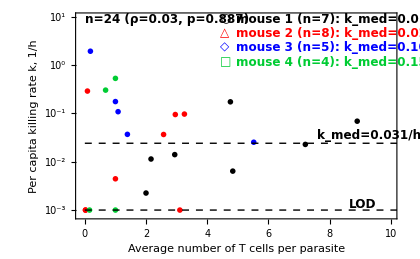

```mathematica
nd=Length[tempdata2];
rho=SpearmanRho[tempdata2][[1,2]];
pval=CorrelationTest[tempdata2,0,"SpearmanRank"];

kmean=Mean[tempdata2[[All,2]]];
kmean2=Mean[10^tempdata2[[All,2]]];
kmed=Median[10^tempdata2[[All,2]]];
tempdata200a=Map[#[[All,{1,2}]]&,tempdata200];
kmedmouse=Map[Median[10^#[[All,2]]]&,tempdata200a];

labs=Table["mouse "<>ToString[i]<>" (n="<>ToString[Length[tempdata200a[[i]]]]<>"): k_med="<>ToString[MyRound[kmedmouse[[i]],3]]<>"/h",{i,1,Length[tempdata200a]}];
myFig1=MyListPlot[tempdata200a,
PlotRange->{{-0.1,10},{-3.1,1}},
FrameLabel->{"Average number of T cells per parasite","Per capita killing rate k, 1/h"},
FrameTicks->{myticks,logticks3[{-3,2,1}]},
Epilog->{
mylegend2noS[{"n="<>ToString[nd]<>" (ρ="<>ToString[MyRound[rho,2]]<>", p="<>ToString[MyRound[pval,3]]<>")"},{-0.02,.97}],
mylegend2[labs,{0.45,0.97}],
mylegend2noS[{"LOD"},{0.8,0.07}],
mylegend2noS[{"k_med="<>ToString[MyRound[kmed,3]]<>"/h"},{0.7,.405}],
{Dashed,Thick,Line[{{0,kmean},{12,kmean}}]},
{Dashed,Line[{{0,-3},{12,-3}}]}
}
]
```

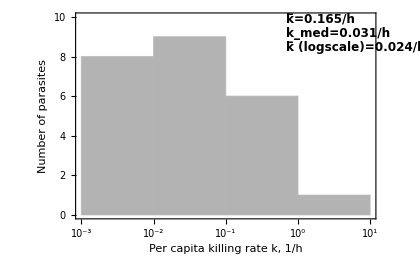

```mathematica
kmean=Mean[tempdata2[[All,2]]];
kmean2=Mean[10^tempdata2[[All,2]]];
kmed=Median[10^tempdata2[[All,2]]];

myFig2=Histogram[tempdata2[[All,2]],
ChartStyle->GrayLevel[0.7],
PlotRange->{0,10},
FrameLabel->{"Per capita killing rate k, 1/h","Number of parasites"},
FrameTicks->{logticks3[{-3,2,1}],myticks},
Epilog->{
mylegend2noS[{"k̄="<>ToString[MyRound[kmean2,3]]<>"/h","k_med="<>ToString[MyRound[kmed,3]]<>"/h",
"k̄ (logscale)="<>ToString[MyRound[10^kmean,3]]<>"/h"},{0.65,.97},FontColor->Table[Black,{3}]]

},
Options[MyPlot]
]
```

```mathematica
1/klow*Log[1/0.2]
1/kmed*Log[1/0.2]
```

11.9218

51.8078

0.5

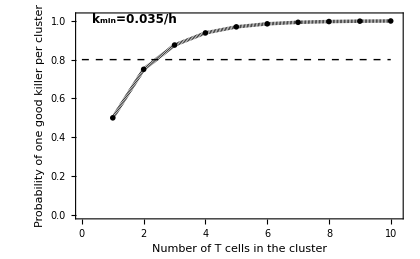

```mathematica
kdist=EmpiricalDistribution[tempdata2[[All,2]]];

klow=0.035;
p0=N[Length[Cases[tempdata2[[All,2]],x_?(#≤Log10[klow]&)]]/Length[tempdata2[[All,2]]]]
tempdata3=Table[{n,1-p0^n},{n,1,10}];

myFig3=MyListPlot[{tempdata3},
PlotRange->{{0,10.2},{0,1.02}},
Joined->True,
FrameLabel->{"Number of T cells in the cluster","Probability of one good killer\nper cluster"},
Epilog->{
{Dashed,Line[{{0,0.80},{10,0.80}}]},
mylegend2noS[{"k_min="<>ToString[MyRound[klow,3]]<>"/h"},{0.,.97}]
}
]
```

```mathematica
allklow={0.0335,0.068,0.135};
tempdata3=Table[
klow=allklow[[k]];
p0=N[Length[Cases[tempdata2[[All,2]],x_?(#≤Log10[klow]&)]]/Length[tempdata2[[All,2]]]];
Table[{n,1-p0^n},{n,1,10}],{k,1,Length[allklow]}];

myFig3=MyListPlot[tempdata3,
PlotRange->{{0,10.2},{0,1.02}},
Joined->True,
FrameLabel->{"Number of T cells in the cluster","Probability of one killer\nwith k>k_min per cluster"},
Epilog->{
{Dashed,Line[{{0,0.80},{10,0.80}}]},
mylegend3[Map["k_min="<>ToString[MyRound[#,3]]<>"/h (T_kill="<>ToString[Round[1/#*Log[1/0.2],3]]<>"h)"&,allklow],{0.35,.25}]
}
]
```

-Graphics-

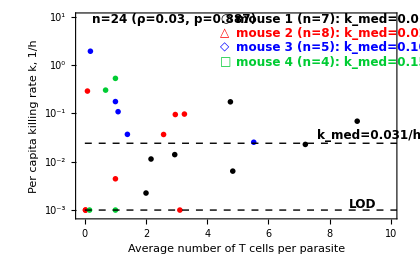
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{myFig1,myFig2,myFig3}

MyGraphicsArray[%];
```

```mathematica
Export["model-percapita-killingrate-vs-Tcellnumber-DDRmodel-24parasites.pdf",%,"PDF"];
```

```mathematica
1/klow*Log[1/0.2]
1/kmed*Log[1/0.2]
```

11.9218

51.8078

```mathematica
(* Making figure of VI dynamics only for parasites with at least one T cell: 24/32 *)

tempdata1=Transpose[{Map[N[Mean[#[[All,2]]]]&,TcellNumber],Map[#[[3,2]]&,AllParsAll],mousenumber}];

allfigsVIs=Cases[Transpose[{tempdata1[[All,1]],allfigsVI}],x_?(#[[1]]>0&):>x[[2]]];

MyGraphicsArray0[Partition[allfigsVIs,UpTo[4]]];
```

```mathematica
Export["fit-VIdynamics-DDRmodel-withTcells-"<>ToString[Length[allfigsVIs]]<>"parasites.pdf",%,"PDF"]
```

/Users/vitaly/research/immunology/malaria/killing-in-clusters/figs/fit-VIdynamics-DDRmodel-withTcells-24parasites.pdf

Simulations

## Varying parasite’s resistance and T cell killing efficacy

### Model 1: full resistance/sensitivity, T cells kill or not

Simulating dynamics of T cell-mediated killing of Plasmodium liver stages. We investigate if variability in observed killing efficacy comes from variability in T cells being able to kill or not, or due to variability in parasite’s resistance to killing. In these simulations, either parasites are resistant to killing or not (0 or 1), and T cells have a given killing efficacy k=0.1/h, with the number of T cells per parasite to vary (Poisson or DD recruitment model?) and the time T cells have to kill to vary (uniform?).

```mathematica
fR=0;  (* probability that a parasite will be resistant to killing *)
fK=0.8; (* probability that a T cell is able to kill *)
k=0.1;   (* 1/h, killing rate by one T cell *)
tmax=4; (* h - duration of T cell interaction with the parasite as observed in experiments *)

nodeath=0;

nT=4;

resistance=RandomInteger[BernoulliDistribution[fR]];
deathrate=k*Total[RandomInteger[BernoulliDistribution[fK],nT]];
dt=RandomReal[UniformDistribution[{0,tmax}]];

deathprob=If[deathrate==0,nodeath,
If[resistance==1,nodeath,
deathtime=RandomReal[ExponentialDistribution[deathrate]];
If[deathtime<tmax,1,0]
]
];
{N[deathprob/tmax],N[deathprob/tmax/(nT*dt/tmax)],dt,deathrate}
```

{0.,0.,1.09445,0.1}

```mathematica
(* function to simulate death of a single parasite *)

Clear[fR,fK,k,tmax,nT];

nodeath=0;

OneParasite[{fR_,fK_,k_,tmax_,nT_}]:=Module[{resistance,deathrate,dt,deathprob},
resistance=RandomInteger[BernoulliDistribution[fR]];
deathrate=k*Total[RandomInteger[BernoulliDistribution[fK],nT]];
dt=RandomReal[UniformDistribution[{0,tmax}]];

deathprob=If[deathrate==0,nodeath,
If[resistance==1,nodeath,
deathtime=RandomReal[ExponentialDistribution[deathrate]];
If[deathtime<tmax,1,0]
]
];
{N[deathprob/tmax],N[deathprob/tmax/(nT*dt/tmax)],dt,deathrate,nT*dt/tmax}
];
```

```mathematica
(* running simulations - vary nT and K *)
nboot=10000;

AllPar0=Table[
{0,0.2,1,1,nT},{nT,1,20}];

SeedRandom[11];

allbootstraps=Map[Table[OneParasite[#],{nboot}]&,AllPar0];
```

```mathematica
(* Save the booststrap simulations *)

Save["simulation-killing-vary-nT-fR-0.txt",{AllPar0,allbootstraps}];
```

```mathematica
(* Analysis of the results *)
boostrapKillRate=Map[#[[All,2]]&,allbootstraps];
Map[Join[{Mean[#]},Quantile[#,{0.025,0.975}]]&,boostrapKillRate]
```

{{1.08947,0.,5.33593},{0.914515,0.,4.6082},{1.46994,0.,4.17946},{0.865108,0.,4.0992},{1.71007,0.,4.38348},{2.4043,0.,3.77022},{0.905284,0.,3.38686},{0.853639,0.,3.43144},{1.33582,0.,2.95119},{1.25616,0.,2.90457},{0.693071,0.,3.14773},{0.757345,0.,2.95551},{0.568577,0.,2.62771},{0.413012,0.,2.28471},{1.16604,0.,2.39751},{0.452787,0.,2.23993},{0.503183,0.,2.14562},{0.685786,0.,2.11966},{0.601196,0.,2.03765},{0.514245,0.,1.90568}}

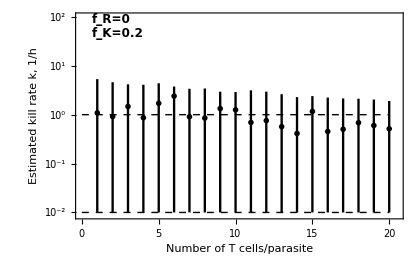

```mathematica
(* Plotting the results *)

tempdata1=Table[{AllPar0[[n,-1]],Around[Mean[boostrapKillRate[[n]]],{Quantile[boostrapKillRate[[n]],0.025]-Mean[boostrapKillRate[[n]]],Quantile[boostrapKillRate[[n]],0.975]-Mean[boostrapKillRate[[n]]]}]},{n,1,Length[AllPar0]}];

tempdata10=Table[{AllPar0[[n,-1]],Around[Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]],{Log10[Max[0.01,Quantile[boostrapKillRate[[n]],0.025]]]-Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]],Log10[Max[0.01,Quantile[boostrapKillRate[[n]],0.975]]]-Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]]}]},{n,1,Length[AllPar0]}];

MyListPlot[{tempdata1},
PlotRange->{-0.05,5},
FrameLabel->{"Number of T cells/parasite","Estimated kill rate k, 1/h"},
IntervalMarkersStyle->{{Black,Thickness[0.004]}},
Epilog->{
{Dashed,Line[{{0,AllPar0[[1,3]]},{Max[AllPar0[[All,-1]]],AllPar0[[1,3]]}}]}
}
];
myFig1a=MyListPlot[{tempdata10},
PlotRange->{{0,20.5},{-2.05,2}},
FrameLabel->{"Number of T cells/parasite","Estimated kill rate k, 1/h"},
IntervalMarkersStyle->{{Black,Thickness[0.004]}},
FrameTicks->{myticks,logticks[{-3,2,1}]},
Epilog->{
mylegend2noS[{"f_R="<>ToString[AllPar0[[1,1]]],"f_K="<>ToString[AllPar0[[1,2]]]},{0,0.97},FontColor->Table[Black,{5}]],
{Dashed,Line[{{0,Log10[AllPar0[[1,3]]]},{Max[AllPar0[[All,-1]]],Log10[AllPar0[[1,3]]]}}]},
{Dashed,Line[{{0,-2},{Max[AllPar0[[All,-1]]],-2}}]}
}
]
```

```mathematica
boostrapKillRate0=Map[#[[All,{-1,2}]]&,allbootstraps];
tempdata3=Map[Map[{#[[1]],Log10[Max[#[[2]],0.01]]}&,#]&,boostrapKillRate0];
tempdata30=Flatten[tempdata3,1];
```

```mathematica
tempdata300=AverageBinnedDataEqual[tempdata30,20][[All,{1,2}]]
```

{{1/2,-0.948421},{3/2,-1.0064},{5/2,-1.00148},{7/2,-1.01122},{9/2,-1.04242},{11/2,-1.05394},{13/2,-1.07469},{15/2,-1.09598},{17/2,-1.11806},{19/2,-1.14207},{21/2,-1.15838},{23/2,-1.17943},{25/2,-1.20586},{27/2,-1.22265},{29/2,-1.24467},{31/2,-1.26049},{33/2,-1.28713},{35/2,-1.30383},{37/2,-1.31326},{39/2,-1.33716}}

```mathematica
(* running simulations - vary nT and fR *)
nboot=10000;

AllPar0=Table[
{0.2,1,1,1,nT},{nT,1,20}];

SeedRandom[22];

allbootstraps=Map[Table[OneParasite[#],{nboot}]&,AllPar0];
```

```mathematica
(* Save the booststrap simulations *)

Save["simulation-killing-vary-nT-fk-1.txt",{AllPar0,allbootstraps}];
```

```mathematica
(* Analysis of the results *)
boostrapKillRate=Map[#[[All,2]]&,allbootstraps];
Map[Join[{Mean[#]},Quantile[#,{0.025,0.975}]]&,boostrapKillRate];
```

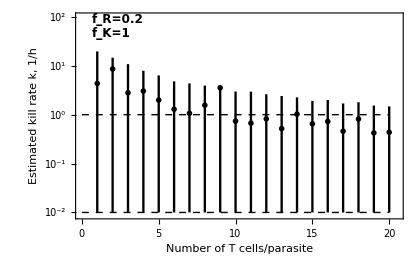

```mathematica
(* Plotting the results *)

tempdata1=Table[{AllPar0[[n,-1]],Around[Mean[boostrapKillRate[[n]]],{Quantile[boostrapKillRate[[n]],0.025]-Mean[boostrapKillRate[[n]]],Quantile[boostrapKillRate[[n]],0.975]-Mean[boostrapKillRate[[n]]]}]},{n,1,Length[AllPar0]}];

tempdata10=Table[{AllPar0[[n,-1]],Around[Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]],{Log10[Max[0.01,Quantile[boostrapKillRate[[n]],0.025]]]-Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]],Log10[Max[0.01,Quantile[boostrapKillRate[[n]],0.975]]]-Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]]}]},{n,1,Length[AllPar0]}];

myFig1b=MyListPlot[{tempdata10},
PlotRange->{{0,20.5},{-2.05,2}},
FrameLabel->{"Number of T cells/parasite","Estimated kill rate k, 1/h"},
IntervalMarkersStyle->{{Black,Thickness[0.004]}},
FrameTicks->{myticks,logticks[{-3,2,1}]},
Epilog->{
mylegend2noS[{"f_R="<>ToString[AllPar0[[1,1]]],"f_K="<>ToString[AllPar0[[1,2]]]},{0,0.97},FontColor->Table[Black,{5}]],
{Dashed,Line[{{0,Log10[AllPar0[[1,3]]]},{Max[AllPar0[[All,-1]]],Log10[AllPar0[[1,3]]]}}]},
{Dashed,Line[{{0,-2},{Max[AllPar0[[All,-1]]],-2}}]}
}
]
```

```mathematica
(* running simulations - vary nT and fK/fR *)

nboot=10000;

AllPar0=Table[
{0.2,0.2,1,1,nT},{nT,1,20}];

SeedRandom[22];

allbootstraps=Map[Table[OneParasite[#],{nboot}]&,AllPar0];
```

```mathematica
(* Save the booststrap simulations *)

Save["simulation-killing-vary-nT-fk-02-fR-02.txt",{AllPar0,allbootstraps}];
```

```mathematica
(* Analysis of the results *)
boostrapKillRate=Map[#[[All,2]]&,allbootstraps];
Map[Join[{Mean[#]},Quantile[#,{0.025,0.975}]]&,boostrapKillRate];
```

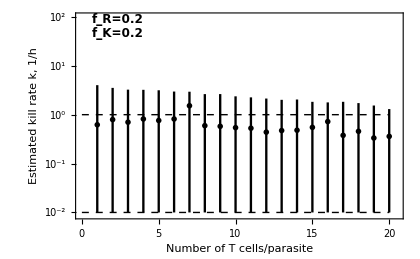

```mathematica
(* Plotting the results *)

tempdata1=Table[{AllPar0[[n,-1]],Around[Mean[boostrapKillRate[[n]]],{Quantile[boostrapKillRate[[n]],0.025]-Mean[boostrapKillRate[[n]]],Quantile[boostrapKillRate[[n]],0.975]-Mean[boostrapKillRate[[n]]]}]},{n,1,Length[AllPar0]}];

tempdata10=Table[{AllPar0[[n,-1]],Around[Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]],{Log10[Max[0.01,Quantile[boostrapKillRate[[n]],0.025]]]-Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]],Log10[Max[0.01,Quantile[boostrapKillRate[[n]],0.975]]]-Log10[Max[0.01,Mean[boostrapKillRate[[n]]]]]}]},{n,1,Length[AllPar0]}];

myFig1c=MyListPlot[{tempdata10},
PlotRange->{{0,20.5},{-2.05,2}},
FrameLabel->{"Number of T cells/parasite","Estimated kill rate k, 1/h"},
IntervalMarkersStyle->{{Black,Thickness[0.004]}},
FrameTicks->{myticks,logticks[{-3,2,1}]},
Epilog->{
mylegend2noS[{"f_R="<>ToString[AllPar0[[1,1]]],"f_K="<>ToString[AllPar0[[1,2]]]},{0,0.97},FontColor->Table[Black,{5}]],
{Dashed,Line[{{0,Log10[AllPar0[[1,3]]]},{Max[AllPar0[[All,-1]]],Log10[AllPar0[[1,3]]]}}]},
{Dashed,Line[{{0,-2},{Max[AllPar0[[All,-1]]],-2}}]}
}
]
```

```mathematica
(* Plotting 3 results *)

{myFig1a,myFig1b,myFig1c}
MyGraphicsArray[%];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["simulations-killrate-estimation-vary-fR-fK-3panels.pdf",%,"PDF"];
```